## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170729";

(*键名直接用短名，里面加上下划线*)
inspiralParams={};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dphi_0] does not exist.

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0005557};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],3]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,80}

输入q范围：{1,10}

m1范围：{3.4461,324.615}

m2范围：{1.21731,91.8959}

对称数据：原始 21859 + 镜像 21859

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.2409×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.2409×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 324.615} × {1.21731, 324.615}

等高线值：{0.0005557}，共 2 条

第一条前3点：{{59.1271,60.1377},{58.825,60.3563},{58.769,60.3969}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.107672

可信水平百分比：10.7672%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.107672

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.446164, 0.553836}

实际使用的 GR 概率区间上下界: {-3.31631, -3.15972}

实际使用的 Param 概率区间上下界: {-3.40612, -3.13777}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=8.43769×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=8.91731×10^-16

Param下界: 点数=500 | Y>0点数=500 | 平均误差=8.6775×10^-16

Param上界: 点数=500 | Y>0点数=500 | 平均误差=8.07354×10^-16

{{40.1,63.2528},{40.2,63.4106},{40.3,63.5683},{40.4,63.726},{40.5,63.8838}}

{{40.1,96.9694},{40.2,97.2112},{40.3,97.4531},{40.4,97.6949},{40.5,97.9367}}

chi1L取值：0.643419

chi2L取值：0.523691

=====================================================

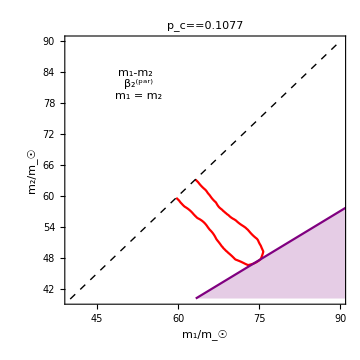

```mathematica
probability=prob;
(*probability=0.4034;*)

plots[p]=PlotInversion[p,probability,40,90,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,150},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0004051};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],3]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,150}

输入q范围：{1,10}

m1范围：{22.974,608.653}

m2范围：{8.11537,172.305}

对称数据：原始 24649 + 镜像 24649

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.13248×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.13248×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{8.11537, 608.653} × {8.11537, 608.653}

等高线值：{0.0004051}，共 2 条

第一条前3点：{{57.7723,55.8956},{58.1269,55.497},{58.3143,55.2915}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.537991

可信水平百分比：53.7991%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.537991

```mathematica
m1m2PDF[p][74,51]
```

0.000729327

```mathematica
ListLinePlot[{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

-Graphics-

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.231005, 0.768995}

实际使用的 GR 概率区间上下界: {-0.000016288, -0.0000134638}

实际使用的 Param 概率区间上下界: {-0.0000239639, -0.0000150899}

GR下界: 点数=220 | Y>0点数=220 | 平均误差=7.54629×10^-22

Greater::nord: Invalid comparison with 10.5-2.46046×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 11.-1.3909×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with 11.5+1.6315×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=220 | Y>0点数=0 | 平均误差=1.42994×10^-6

Param下界: 点数=220 | Y>0点数=220 | 平均误差=7.01343×10^-6

Param上界: 点数=220 | Y>0点数=220 | 平均误差=1.21665×10^-21

{{10.5,2.08159×10^6},{11.,2.1807×10^6},{11.5,2.27983×10^6},{12.,2.37896×10^6},{12.5,2.47807×10^6}}

{{10.5,5.25863},{11.,5.50904},{11.5,5.75945},{12.,6.00986},{12.5,6.26027}}

chi1L取值：0.592901

chi2L取值：0.51105

=====================================================

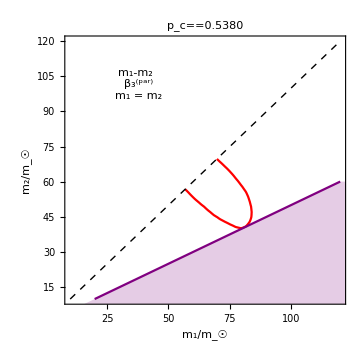

```mathematica
probability=prob;
(*probability=0.5;*)

(* 蓝色要对称一下 *)
plots[p]=PlotInversion[p,probability,10,120,0.5,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],3]}]
```

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00007};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 23410 + 镜像 23410

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.17901×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.17902×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00007}，共 2 条

第一条前3点：{{43.4645,44.4642},{43.4631,44.4649},{43.3422,44.5977}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.9425

可信水平百分比：94.25%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.9425

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.9063;


PlotInversion[p,probability,10,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.04685, 0.95315}

实际使用的 GR 概率区间上下界: {-0.0870497, -0.0537994}

实际使用的 Param 概率区间上下界: {-0.198135, -0.0694716}

Greater::nord: Invalid comparison with -0.517892-9.10815 ⅈ attempted.

Greater::nord: Invalid comparison with -0.564973-9.93616 ⅈ attempted.

Greater::nord: Invalid comparison with -0.612054-10.7642 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=90 | Y>0点数=0 | 平均误差=1.20702×10^-16

GR上界: 点数=90 | Y>0点数=90 | 平均误差=1.67304×10^-17

Param下界: 点数=90 | Y>0点数=0 | 平均误差=1.84133×10^-16

Param上界: 点数=90 | Y>0点数=90 | 平均误差=4.30211×10^-17

{{11,-11.9636+19.2351 ⅈ},{12,-13.0512+20.9837 ⅈ},{13,-14.1388+22.7324 ⅈ},{14,-15.2264+24.481 ⅈ},{15,-16.314+26.2297 ⅈ}}

{{11,10.9644},{12,11.9612},{13,12.9579},{14,13.9547},{15,14.9514}}

chi1L取值：0.425342

chi2L取值：0.453012

=====================================================

-Graphics-

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],3]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 19484 + 镜像 19484

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.76198×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.76198×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0005}，共 2 条

第一条前3点：{{50.6053,51.607},{50.3148,51.8926},{50.2804,51.9261}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.595825

可信水平百分比：59.5825%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.595825

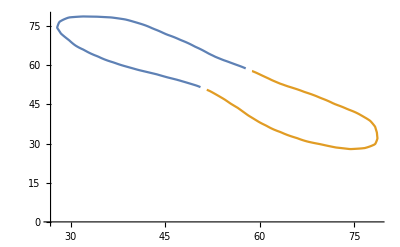

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
m1m2PDF[p][67,41]
```

0.00102046

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0275, 0.9725}

实际使用的 GR 概率区间上下界: {-47.9653, -7.97959}

实际使用的 Param 概率区间上下界: {-327.966, -25.8903}

GR下界: 点数=60 | Y>0点数=2 | 平均误差=0.734489

GR上界: 点数=60 | Y>0点数=60 | 平均误差=3.25073×10^-14

Param下界: 点数=60 | Y>0点数=0 | 平均误差=1.76215×10^-13

Param上界: 点数=60 | Y>0点数=60 | 平均误差=2.92507×10^-14

{{31,-98.966},{32,-102.158},{33,-105.351},{34,-108.543},{35,-111.736}}

{{31,30.2185},{32,31.1933},{33,32.1681},{34,33.1428},{35,34.1176}}

chi1L取值：0.361445

chi2L取值：0.468486

=====================================================

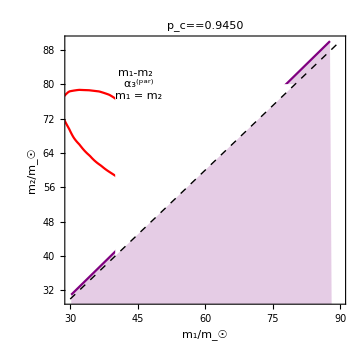

```mathematica
probability=prob;
probability=0.9450;
(*probability=0.93;*)

PlotInversion[p,probability,30,90,1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 24656 + 镜像 24656

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.34909×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.34909×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0002}，共 2 条

第一条前3点：{{51.4717,52.4706},{51.4703,52.4721},{51.4192,52.5213}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.831741

可信水平百分比：83.1741%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.831741

```mathematica
m1m2PDF[p][72,40]
```

0.00111618

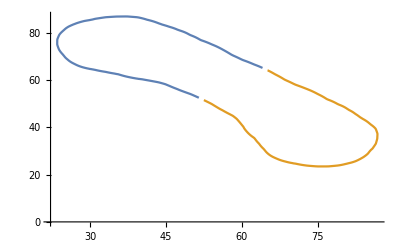

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.03055, 0.96945}

实际使用的 GR 概率区间上下界: {0.201979, 0.276549}

实际使用的 Param 概率区间上下界: {0.269359, 0.929695}

GR下界: 点数=600 | Y>0点数=600 | 平均误差=3.26591×10^-17

GR上界: 点数=600 | Y>0点数=600 | 平均误差=0.00718086

Param下界: 点数=600 | Y>0点数=600 | 平均误差=2.48875×10^-17

Param上界: 点数=600 | Y>0点数=600 | 平均误差=0.660326

{{30.1,31.3012},{30.2,31.4052},{30.3,31.5092},{30.4,31.6132},{30.5,31.7172}}

{{30.1,30.9213},{30.2,31.0253},{30.3,31.1268},{30.4,31.2296},{30.5,31.3328}}

chi1L取值：0.762274

chi2L取值：0.0870202

=====================================================

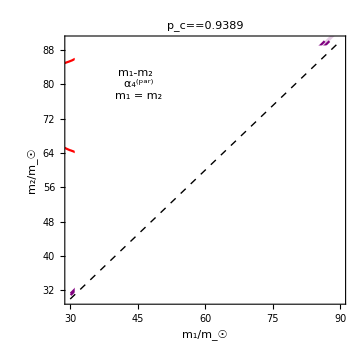

```mathematica
probability=prob;
(*probability=0.95;*)
probability=0.9389;

PlotInversion[p,probability,30,90,0.1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.9,spinPercentile2->0.1,contourIndices->{1}]
```

# Total plots

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dbeta_2.pdf ...

正在导出矢量图: plot_dbeta_3.pdf ...